```mathematica
ClearAll["Global`*"]
```

```mathematica
a = {1,10000,1};
a0 = Total[a];
mu = {-15,-15,-15};
sig = {1,1,1};
nprey = Length[a];

VarZ =N[Sum[a[[i]]/a0(sig[[i]]^2+mu[[i]]^2) - (a[[i]]^2 *mu[[i]]^2)/a0^2,{i,1,nprey}] - Sum[(a[[i]]*a[[j]]*mu[[i]]*mu[[j]])/a0^2 Boole[i≠j],{i,1,nprey},{j,1,nprey}]]
```

1.

```mathematica
1.21^2
```

1.4641

```mathematica
Manipulate[
VarZ=Table[
a = {1,a2,1};
a0 = Total[a];
mu = {-15,mean2,-15};
sig = {1,500,1};
nprey = Length[a];
{a2/a0,N[Sum[a[[i]]/a0(sig[[i]]^2+mu[[i]]^2) - (a[[i]]^2 *mu[[i]]^2)/a0^2,{i,1,nprey}] - Sum[(a[[i]]*a[[j]]*mu[[i]]*mu[[j]])/a0^2 Boole[i≠j],{i,1,nprey},{j,1,nprey}]]},
{a2,1,100,0.1}];
Show[{
ListPlot[VarZ,PlotRange->{{0,1},{0,100}},Joined->True],
Graphics[Line[{{0,Max[VarZ[[All,2]]]},{1,Max[VarZ[[All,2]]]}}]]
}]
,{mean2,-15,0}]
```

```mathematica
VarZ[[All,2]]
```

```mathematica
VarZ=(1-s)/(n-1)*A + s*B - ((1-s)/(n-1)*c + s*d)^2
Ds = D[VarZ,s]
```

(A (1-s))/(-1+n)+B s-((c (1-s))/(-1+n)+d s)^2

B-A/(-1+n)-2 (d-c/(-1+n)) ((c (1-s))/(-1+n)+d s)

```mathematica
Ssol2 = s/.FullSimplify[Solve[Ds==0,s]]
```

{(A+B (-1+n)^2-A n+2 c (c+d-d n))/(2 (c+d-d n)^2)}

```mathematica
S=((A/(n-1)-B)/(2*(c/(n-1)-d))- 1/(n-1))/(d -c/(n-1))
```

((-B+A/(-1+n))/(2 (-d+c/(-1+n)))-1/(-1+n))/(d-c/(-1+n))

```mathematica
Ssol =FullSimplify[S]
```

(A+B+2 (c+d)-(A+2 (B+d)) n+B n^2)/(2 (c+d-d n)^2)

Basic plot of the variance function with specialization parameter

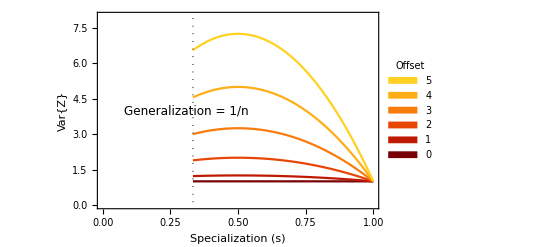

```mathematica
mu = {-15,-15+offset,-15};
sig = {1,1,1};
nprey = Length[mu];
preyk=2;
VarZ=(1-sk)/(nprey-1)*Sum[(sig[[i]]^2 + mu[[i]]^2)Boole[i≠ preyk],{i,1,nprey}]+sk*(mu[[preyk]]^2+sig[[preyk]]^2)-((1-sk)/(nprey-1)*Sum[(mu[[i]])Boole[i≠ preyk],{i,1,nprey}]+sk*mu[[preyk]])^2;
VarZsol = Table[VarZ/.{offset->x},{x,0,5,1}];
VarFig=
Show[{
Plot[VarZsol,{sk,1/nprey,1},Frame->True,PlotRange->{{0,1},{0,8}},AxesOrigin->{0,0},
FrameLabel->{"Specialization (s)","Var{Z}"},PlotStyle->"SolarColors",
PlotLegends->SwatchLegend[Table[x,{x,0,5,1}],LegendLabel->"Offset",LegendLayout->{"ReversedColumn",1},LegendMarkers->"Bubble"]],
Graphics[{Dotted,Line[{{1/nprey,-10},{1/nprey,20}}]}],
Graphics[Rotate[Text[Style["Generalization = 1/n",FontSize->12],{1/nprey-0.025,4}],90Degree]]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_var.pdf",VarFig]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_var.pdf

Analysis of Inflexion point

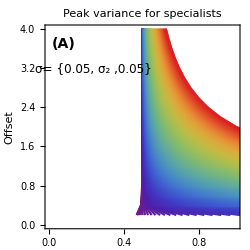
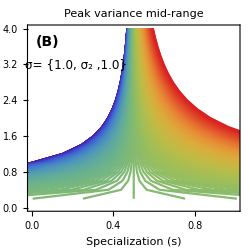
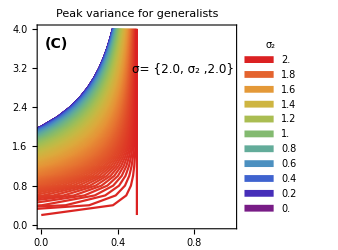
-Graphics- | -Graphics- | -Graphics-

```mathematica
ColorBar=ImageResize[Image[ColorData["Rainbow","Image"]],{20,20}];
VarZ=(1-s)/(n-1)*A + s*B - ((1-s)/(n-1)*c + s*d)^2;
Ds = D[VarZ,s];
Ssol2 = s/.FullSimplify[Solve[Ds==0,s]];
VarSpecFig =Grid[{
Flatten[{
mtable=
Table[
Table[
mu = {-15,-15+offset,-15};
sig = {0.05,s2,0.05};
nprey = Length[mu];
prey1 = 2;
FullSsol = Ssol2/.{
n->nprey,
A->Sum[(sig[[i]]^2 + mu[[i]]^2)Boole[i≠prey1],{i,1,nprey}],
B->(sig[[prey1]]^2 + mu[[prey1]]^2),
c->Sum[mu[[i]]Boole[i≠prey1],{i,1,nprey}],
d-> mu[[prey1]]
};
Flatten[{N[FullSsol],offset}],
{offset,0.2,10,0.2}],
{s2,0,2,0.01}];
(*DisplayText = {sig[[1]],ColorBar,sig[[3]]};*)
Show[{
ListPlot[mtable,Joined->True,Frame->True,PlotStyle->"Rainbow",PlotRange->{{0,1},{0,4}},ImageSize->250,FrameLabel->{"",Style["Offset",FontSize->14]},AspectRatio->1,PlotLabel->"Peak variance for specialists"],
Graphics[Text[Style["σ= {0.05, σ_2 ,0.05}",FontSize->12],{0.24,3.2}]],
(*Graphics[Inset[Rasterize[DisplayText,ImageSize->90,ImageResolution->600],{0.22,3.5}]]*)
(*Graphics[Inset[Rasterize[ColorBar,ImageSize->15],{0.275,3.5}]],*)
Graphics[Text[Style["(A)",Bold,FontSize->14],{0.08,3.7}]]
}],
mtable=
Table[
Table[
mu = {-15,-15+offset,-15};
sig = {1,s2,1};
nprey = Length[mu];
prey1 = 2;
FullSsol = Ssol2/.{
n->nprey,
A->Sum[(sig[[i]]^2 + mu[[i]]^2)Boole[i≠prey1],{i,1,nprey}],
B->(sig[[prey1]]^2 + mu[[prey1]]^2),
c->Sum[mu[[i]]Boole[i≠prey1],{i,1,nprey}],
d-> mu[[prey1]]
};
Flatten[{N[FullSsol],offset}],
{offset,0.2,10,0.2}],
{s2,0,2,0.01}];
Show[{
ListPlot[mtable,Joined->True,Frame->True,PlotStyle->"Rainbow",PlotRange->{{0,1},{0,4}},ImageSize->250,
FrameLabel->{Style["Specialization (s)",FontSize->12],""},PlotLabel->"Peak variance mid-range",AspectRatio->1],
Graphics[Text[Style["σ= {1.0, σ_2 ,1.0}",FontSize->12],{0.22,3.2}]],
(*Graphics[Inset[Rasterize[DisplayText,ImageSize->90,ImageResolution->600],{0.22,3.5}]]*)
(*Graphics[Inset[Rasterize[ColorBar,ImageSize->15],{0.275,3.5}]],*)
Graphics[Text[Style["(B)",Bold,FontSize->14],{0.08,3.7}]]
}],
mtable=
Table[
Table[
mu = {-15,-15+offset,-15};
sig = {2,s2,2};
nprey = Length[mu];
prey1 = 2;
FullSsol = Ssol2/.{
n->nprey,
A->Sum[(sig[[i]]^2 + mu[[i]]^2)Boole[i≠prey1],{i,1,nprey}],
B->(sig[[prey1]]^2 + mu[[prey1]]^2),
c->Sum[mu[[i]]Boole[i≠prey1],{i,1,nprey}],
d-> mu[[prey1]]
};
Flatten[{N[FullSsol],offset}],
{offset,0.2,10,0.2}],
{s2,0,2,0.01}];
Show[{
ListPlot[mtable,Joined->True,Frame->True,PlotStyle->"Rainbow",PlotRange->{{0,1},{0,4}},FrameLabel->{"",""},PlotLegends->SwatchLegend["Rainbow",Table[σ,{σ,0,2,0.2}],LegendLabel->"σ_2",LegendFunction->(#&),LegendMargins->1,LegendLayout->{"ReversedColumn",1},LegendMarkers->"Bubble"],ImageSize->250,AspectRatio->1,PlotLabel->"Peak variance for generalists"],
Graphics[Text[Style["σ= {2.0, σ_2 ,2.0}",FontSize->12],{0.74,3.2}]],
(*Graphics[Inset[Rasterize[DisplayText,ImageSize->90,ImageResolution->600],{0.22,3.5}]]*)
(*Graphics[Inset[Rasterize[ColorBar,ImageSize->15],{0.775,3.5}]],*)
Graphics[Text[Style["(C)",Bold,FontSize->14],{0.08,3.7}]]
}]
}]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_specvar.pdf",VarSpecFig]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_specvar.pdf

0) Parabola is always upside down... there is always a ‘peak variance’... often it is within specialization= [0,1]
1) Distribution of variances determines whether the peak is on the left (generalists have higher variance) or on the right (specialists have higher variances)
2) Across offset values for the ‘specialized prey’, the peak tends to be in the middle; this means the moderate specialist has higher variance